## The Laplace Transform and Applications Section 7.3 Exercises 1. (i)

```mathematica
LaplaceTransform[t*Exp[-7t], t,s]
```

1/(7+s)^2

## (ii)

```mathematica
LaplaceTransform[t^2*Exp[-7t], t,s]
```

2/(7+s)^3

## (iii)

```mathematica
LaplaceTransform[t*Cos[2t], t,s]
TeXForm[%]
```

(-4+s^2)/((4+s^2)^2)

\frac{s^2-4}{\left(s^2+4\right)^2}

## (iv)

```mathematica
LaplaceTransform[t^2*Cos[2t], t,s]
TeXForm[%]
```

(2 s (-12+s^2))/((4+s^2)^3)

\frac{2 s \left(s^2-12\right)}{\left(s^2+4\right)^3}

## (v)

```mathematica
LaplaceTransform[t Exp[-3t]Cos[2t], t,s]
TeXForm[%]
```

(5+6 s+s^2)/((13+6 s+s^2)^2)

\frac{s^2+6 s+5}{\left(s^2+6 s+13\right)^2}

## (vi)

```mathematica
LaplaceTransform[t^2 Exp[-3t]Cos[2t], t,s]
TeXForm[%]
```

(2 (3+s) (-3+6 s+s^2))/((13+6 s+s^2)^3)

\frac{2 (s+3) \left(s^2+6 s-3\right)}{\left(s^2+6 s+13\right)^3}

## (vii)

```mathematica
LaplaceTransform[t Exp[3t]Sin[5t], t,s]
TeXForm[%]
```

(10 (-3+s))/((34-6 s+s^2)^2)

\frac{10 (s-3)}{\left(s^2-6 s+34\right)^2}

## 2.

```mathematica
LaplaceTransform[(Exp[-t]-1)/t, t,s]
TeXForm[%]
```

Log[s/(1+s)]

\log \left(\frac{s}{s+1}\right)

## 3.

```mathematica
LaplaceTransform[(Exp[-t]-2)/t, t,s]
TeXForm[%]
```

LaplaceTransform[(-2+ⅇ^-t)/t,t,s]

\mathcal{L}_t\left[\frac{e^{-t}-2}{t}\right](s)

```mathematica
F[s_]:=LaplaceTransform[Exp[-t]-2, t, s]
F[s]
Integrate[F[s], {s, s, Infinity}]
TeXForm[%]
```

-2/s+1/(s+Log[e])

Integrate::idiv: Integral of -2/s+1/(s+Log[e]) does not converge on {s,∞}.

∫_s^∞ (-2/s+1/(s+Log[e]))ⅆs

\int_s^{\infty } \left(\frac{1}{\log (e)+s}-\frac{2}{s}\right) \, ds

## 4(i)

y[t]+y'[t]==t Cos[t]

{y[0]==0}

{{y→Function[{t},1/2 (t Cos[t]-Sin[t]+t Sin[t])]}}

{{y→Function[{t},1/2 (t Cos[t]-Sin[t]+t Sin[t])]}}

True

0

0

{1/2 (t Cos[t]-Sin[t]+t Sin[t])}

{1/2 (t Cos[t]+(-1+t) Sin[t])}

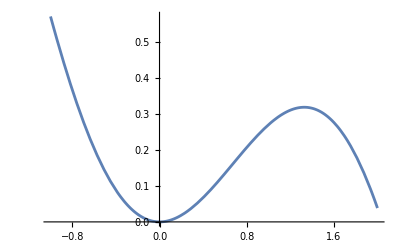

\left\{\frac{1}{2} ((t-1) \sin (t)+t \cos (t))\right\}

```mathematica
Clear[Derivative]
DE=y'[t]+y[t] == t*Cos[t]
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## 4(ii).

-y[t]+y'[t]==ⅇ^t t Cos[t]

{y[0]==0}

{{y→Function[{t},ⅇ^t (-1+Cos[t]+t Sin[t])]}}

{{y→Function[{t},ⅇ^t (-1+Cos[t]+t Sin[t])]}}

True

0

0

{ⅇ^t (-1+Cos[t]+t Sin[t])}

{ⅇ^t (-1+Cos[t]+t Sin[t])}

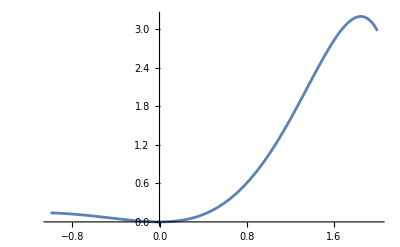

\left\{e^t (t \sin (t)+\cos (t)-1)\right\}

```mathematica
Clear[Derivative]
DE=y'[t]-y[t] == t*Exp[t]*Cos[t]
IC={y[0]==0}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

## 4(iii).

```mathematica
Clear[Derivative]
DE=y''[t]+4y[t] == Cos[2t]
IC={y[0]==2, y'[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,2}]
```

4 y[t]+y''[t]==Cos[2 t]

{y[0]==2,y'[0]==1}

{{y→Function[{t},1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])]}}

{{y→Function[{t},1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])]}}

True

2

1

{1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])}

{2 Cos[2 t]+1/4 (2+t) Sin[2 t]}

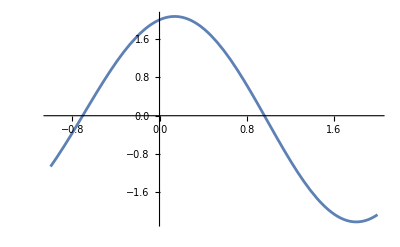
## 

\left\{\frac{1}{4} (t+2) \sin (2 t)+2 \cos (2 t)\right\}

## 4 (iv) .

4 y[t]+y''[t]==Cos[2 t] (1-UnitStep[-2 π+t])

{y[0]==2,y'[0]==1}

{{y→Function[{t},1/2 (4 Cos[2 t]+Sin[2 t]+π Sin[2 t])+(1/2 (-4 Cos[2 t]-Sin[2 t]-π Sin[2 t])+1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])) UnitStep[2 π-t]]}}

{{y→Function[{t},1/2 (4 Cos[2 t]+Sin[2 t]+π Sin[2 t])+(1/2 (-4 Cos[2 t]-Sin[2 t]-π Sin[2 t])+1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])) UnitStep[2 π-t]]}}

t≠2 π

2

1+1/2 (-2-2 π)+1/2 (2+2 π)

{1/2 (4 Cos[2 t]+Sin[2 t]+π Sin[2 t])+(1/2 (-4 Cos[2 t]-Sin[2 t]-π Sin[2 t])+1/16 (31 Cos[2 t]+Cos[2 t] Cos[4 t]+8 Sin[2 t]+4 t Sin[2 t]+Sin[2 t] Sin[4 t])) UnitStep[2 π-t]}

{Piecewise[{{2 Cos[2 t]+(1+π) Cos[t] Sin[t], t>2 π}, {2 Cos[2 t]+1/4 (2+t) Sin[2 t], True}}]}

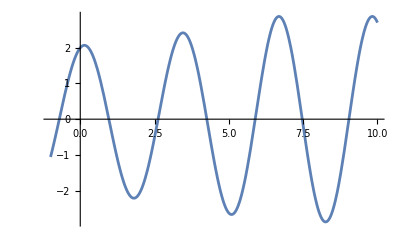

\left\{
\begin{array}{cc}
 \{ & 
\begin{array}{cc}
 2 \cos (2 t)+(1+\pi ) \cos (t) \sin (t) & t>2 \pi  \\
 2 \cos (2 t)+\frac{1}{4} (t+2) \sin (2 t) & \text{True} \\
\end{array}
 \\
\end{array}
\right\}

```mathematica
Clear[Derivative]
DE=y''[t]+4y[t] == Cos[2t]*(1- UnitStep[t-2Pi])
IC={y[0]==2, y'[0]==1}
Gensol = DSolve[{DE, IC}, y, t]
Parsol=DSolve[{DE,IC},y,t]
DE/. Parsol[[1]]//Simplify
y[0]/. Parsol[[1]]
y'[0]/. Parsol[[1]]
y[t]/. Parsol
Simplify[%]
TeXForm[%]
Plot[y[t]/. Parsol,{t,-1,10}]
```